## 经典物理学的本质

## 空间、三角学和矢量

### 练习4

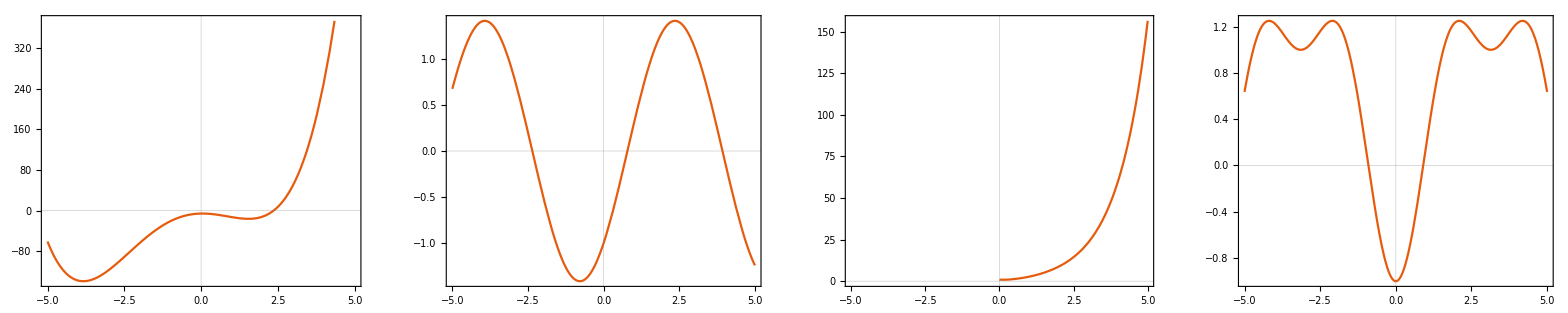

```mathematica
Plot[#,{t,-5,5},PlotTheme->"Scientific"]&/@{t^4+3t^3-12t^2+t-6,Sin[t]-Cos[t],Exp[t]+t Log[t],Sin[t]^2-Cos[t]}//GraphicsRow[#,ImageSize->Full]&
```

### 练习7

```mathematica
{Norm[#[[1]]],Norm[#[[2]]],Dot[#[[1]],#[[2]]],VectorAngle[#[[1]],#[[2]]]}&@{{2,-3,1},{-4,-3,2}}
N[%]
```

{√14,√29,3,ArcCos[3/(√406)]}

{3.74166,5.38516,3.,1.42135}

### 练习8

```mathematica
Subsets[{{1,1,1},{2,-1,3},{3,1,0},{-3,0,2}},{2}](*向量两两组合*)
Dot@@@%(*组合后作点积，确定正交向量*)
```

{{{1,1,1},{2,-1,3}},{{1,1,1},{3,1,0}},{{1,1,1},{-3,0,2}},{{2,-1,3},{3,1,0}},{{2,-1,3},{-3,0,2}},{{3,1,0},{-3,0,2}}}

{4,4,-1,5,0,-9}

## 运动

## 微分学

### 练习1

```mathematica
D[#,t]&/@{t^4+3t^3-12t^2+t-6,Sin[t]-Cos[t],Exp[t]+t Log[t],Sin[t]^2-Cos[t]}
```

{1-24 t+9 t^2+4 t^3,Cos[t]+Sin[t],1+ⅇ^t+Log[t],Sin[t]+2 Cos[t] Sin[t]}

### 练习2

```mathematica
D[#,{t,2}]&/@{t^4+3t^3-12t^2+t-6,Sin[t]-Cos[t],Exp[t]+t Log[t],Sin[t]^2-Cos[t]}
```

{-24+18 t+12 t^2,Cos[t]-Sin[t],ⅇ^t+1/t,Cos[t]+2 Cos[t]^2-2 Sin[t]^2}

## 质点运动

### 练习8

```mathematica
{va,vb,vc,vd}={#,D[#,t],D[#,{t,2}]}(*位置、速度、加速度*)&/@{{Cos[ω t],Exp[ω t]},{Cos[ω t-ϕ],Sin[ω t-ϕ]},{c Cos[t]^3,c Sin[t]^3},{c(t-Sin[t]),c(1-Cos[t])}}
```

{{{Cos[t ω],ⅇ^(t ω)},{-ω Sin[t ω],ⅇ^(t ω) ω},{-ω^2 Cos[t ω],ⅇ^(t ω) ω^2}},{{Cos[ϕ-t ω],-Sin[ϕ-t ω]},{ω Sin[ϕ-t ω],ω Cos[ϕ-t ω]},{-ω^2 Cos[ϕ-t ω],ω^2 Sin[ϕ-t ω]}},{{c Cos[t]^3,c Sin[t]^3},{-3 c Cos[t]^2 Sin[t],3 c Cos[t] Sin[t]^2},{c (-3 Cos[t]^3+6 Cos[t] Sin[t]^2),c (6 Cos[t]^2 Sin[t]-3 Sin[t]^3)}},{{c (t-Sin[t]),c (1-Cos[t])},{c (1-Cos[t]),c Sin[t]},{c Sin[t],c Cos[t]}}}

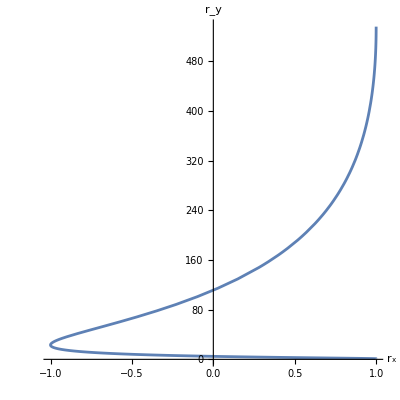
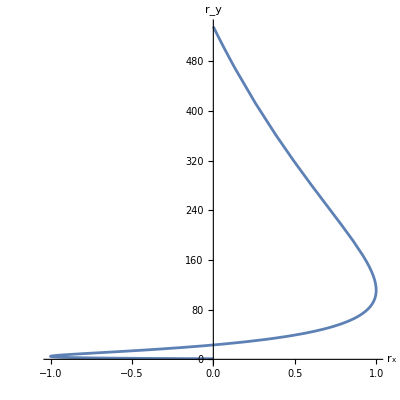
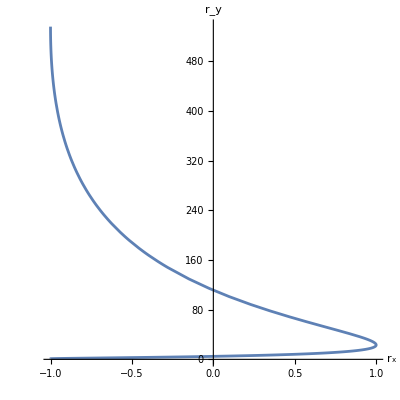
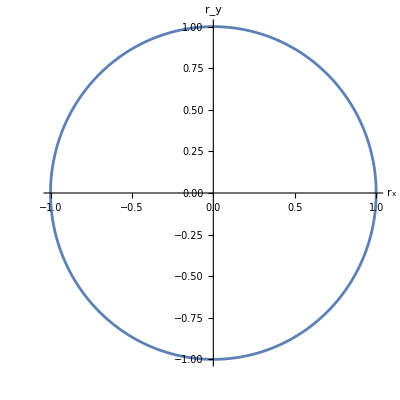
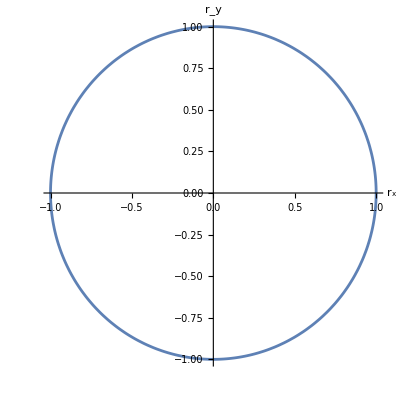
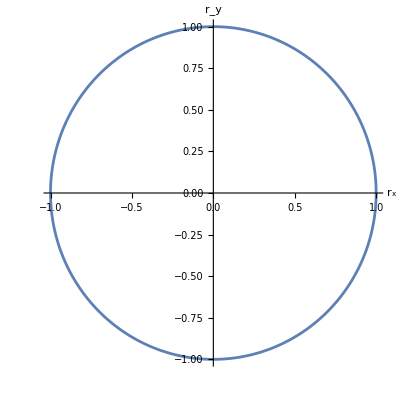
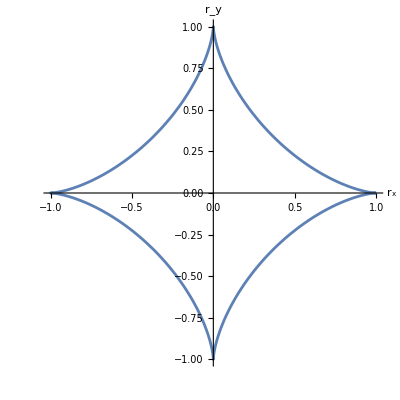
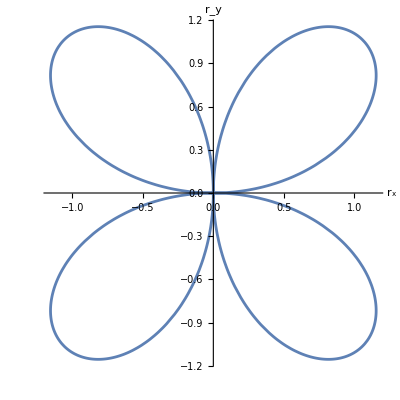

```mathematica
ParametricPlot[#/.{ω->1,ϕ->0,c->1},{t,0,2Pi},AspectRatio->1,AxesLabel->{Subscript[r, x],Subscript[r, y]}]&/@#&/@{va,vb,vc,vd}
```

## 积分

### 练习9

```mathematica
Integrate[#,t,GeneratedParameters->C]&/@{t^4,Cos[t],t^2-2}
```

{t^5/5+C[1],C[1]+Sin[t],-2 t+t^3/3+C[1]}

### 练习10

```mathematica
Integrate[#,{t,0,T}]&/@{t^4,Cos[t],t^2-2}
```

{T^5/5,Sin[T],-2 T+T^3/3}

### 练习12

```mathematica
Integrate[x Cos[x],{x,0,Pi/2}]//Expand
```

-1+π/2

## 动力学

### 练习4

```mathematica
DSolve[x''[t]==-ω^2 x[t],x[t],t]
```

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

## 偏微分

### 练习5

```mathematica
{D[#,x],D[#,y],D[#,{x,2}],D[#,{y,2}],D[D[#,x],y]}(*一二阶及混合偏导*)&/@{x^2+y^2-Sin[x y],x/y(Exp[x^2]+y^2),Exp[x]Cos[y]}
```

{{2 x-y Cos[x y],2 y-x Cos[x y],2+y^2 Sin[x y],2+x^2 Sin[x y],-Cos[x y]+x y Sin[x y]},{(2 ⅇ^(x^2) x^2)/y+(ⅇ^(x^2)+y^2)/y,2 x-(x (ⅇ^(x^2)+y^2))/y^2,(4 ⅇ^(x^2) x)/y+(x (2 ⅇ^(x^2)+4 ⅇ^(x^2) x^2))/y,-(2 x)/y+(2 x (ⅇ^(x^2)+y^2))/y^3,2-(2 ⅇ^(x^2) x^2)/y^2-(ⅇ^(x^2)+y^2)/y^2},{ⅇ^x Cos[y],-ⅇ^x Sin[y],ⅇ^x Cos[y],-ⅇ^x Cos[y],-ⅇ^x Sin[y]}}

### 练习6

如果海森矩阵的行列式和迹是正数，那么驻点对应局部极小值。

如果行列式是正数，迹是负数，那么驻点对应局部极大值。

如果行列式是负数，那么无论迹是正是负，驻点都对应鞍点。

```mathematica
{Det[#],Tr[#]}&@ResourceFunction["HessianMatrix"][#,{x,y}]&/@{Sin[x]+Sin[y],Cos[x]+Cos[y]}
%/.{{x->Pi/2,y->-Pi/2},{x->-Pi/2,y->Pi/2},{x->-Pi/2,y->-Pi/2}}
```

{{Sin[x] Sin[y],-Sin[x]-Sin[y]},{Cos[x] Cos[y],-Cos[x]-Cos[y]}}

{{{-1,0},{0,0}},{{-1,0},{0,0}},{{1,2},{0,0}}}

```mathematica
Plot3D[#,{x,-Pi,Pi},{y,-Pi,Pi},PlotRange->All,MeshFunctions->{#3&},MeshStyle->Directive[Red,PointSize[0.03]]]&/@{Sin[x]+Sin[y],Cos[x]+Cos[y]}
```

{-Graphics3D-,-Graphics3D-}